## Import data

```mathematica
ClearAll["Global`*"]
```

```mathematica
parampath="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/wobbling-ba130/fit_params.dat";
band1path="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/wobbling-ba130/ba_130_B1_band.dat";
band2path="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/wobbling-ba130/ba_130_B2_band.dat";
```

```mathematica
params=Flatten[Import[parampath]];
dataBand1=Import[band1path];
dataBand2=Import[band2path];
```

```mathematica
spinsband1=Table[dataBand1[[i,1]],{i,1,Length[dataBand1]}];
spinsband2=Table[dataBand2[[i,1]],{i,1,Length[dataBand2]}];
band1exp=Table[dataBand1[[i,2]],{i,1,Length[dataBand1]}];
band2exp=Table[dataBand2[[i,2]],{i,1,Length[dataBand2]}];
band1th=Table[dataBand1[[i,3]],{i,1,Length[dataBand1]}];
band2th=Table[dataBand2[[i,3]],{i,1,Length[dataBand2]}];
```

```mathematica
bandmaker[start_,shift_,energies_]:=Table[{{start,energies[[i]]},{start+shift,energies[[i]]}},{i,1,Length[energies]}];
energyplotter[energies_,color_]:=ListLinePlot[energies,Axes->{False,True,False,False},Frame->None,AxesStyle->Directive[Black,Thick],ImageSize->350,AspectRatio->1.4,PlotStyle->Directive[Thick,color],AxesLabel->{"","E [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"}];
shower[energiesexp_,energiesth_,spins_,color_,band_]:=Show[energyplotter[bandmaker[1,1,energiesexp],Black],energyplotter[bandmaker[2.3,1,energiesth],color],PlotRange->{Full,{Min[energiesexp]-1.5,Max[energiesexp]+0.3}},Epilog->{Table[Inset[Style[StringTemplate["(``)^+"][spins[[i]]],Black,17,Bold,Italic],{1.5,energiesexp[[i]]+0.25}],{i,1,Length[energiesexp]}],Table[Inset[Style[StringTemplate["(``)^+"][spins[[i]]],Black,17,Bold,Italic],{2.8,energiesth[[i]]+0.25}],{i,1,Length[energiesth]}],Inset[Style["Exp.",Black,Bold,17],{1.5,-.5}],Inset[Style["Th.",Black,Bold,17],{2.8,-.5}],Inset[Framed[Style[band,Black,Italic,Bold,17]],{2.1,-.5}]}];
plot1=shower[band1exp,band1th,spinsband1,Red,"B1"];
plot2=shower[band2exp,band2th,spinsband2,Blue,"B2"];
(*Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-ba130/ba130-band1.pdf",plot1,ImageResolution->1200];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-ba130/ba130-band2.pdf",plot2,ImageResolution->1200];*)
```

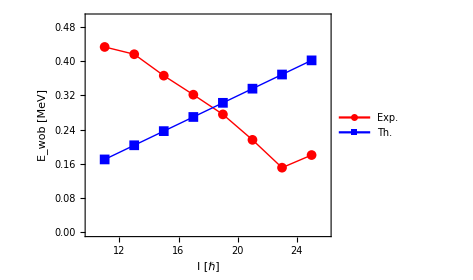

```mathematica
wobblingexp=Table[If[i==1,{spinsband2[[i]],band2exp[[i]]-1/2 band1exp[[i]]},{spinsband2[[i]],(band2exp[[i]])-1/2((band1exp[[i-1]])+(band1exp[[i]]))}],{i,1,Length[band2exp]}];
wobblingth=Table[If[i==1,{spinsband2[[i]],band2th[[i]]-1/2 band1th[[i]]},{spinsband2[[i]],(band2th[[i]])-1/2((band1th[[i-1]])+(band1th[[i]]))}],{i,1,Length[band2th]}];
wobblingPlot=ListPlot[{wobblingexp,wobblingth},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,Joined->True,PlotMarkers->{Automatic, Medium},FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLegends->Placed[{"Exp.","Th."},Scaled[{0.25,0.2}]],PlotRange->{{10,26},{0,0.5}},ImageSize->350];
Export["/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/wobbling-ba130/ba130-wobbling-energies.pdf",wobblingPlot,ImageResolution->1200];
Show[wobblingPlot]
```

## computing the rotational frequency

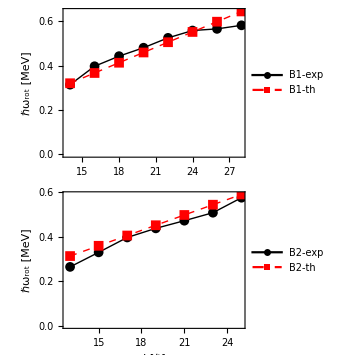

```mathematica
rotfreqexp1=Table[{spinsband1[[i]],1/2(band1exp[[i]]-band1exp[[i-1]])},{i,2,Length[band1exp]}];
rotfreqexp2=Table[{spinsband2[[i]],1/2(band2exp[[i]]-band2exp[[i-1]])},{i,2,Length[band2exp]}];
rotfreqth1=Table[{spinsband1[[i]],1/2(band1th[[i]]-band1th[[i-1]])},{i,2,Length[band1th]}];
rotfreqth2=Table[{spinsband2[[i]],1/2(band2th[[i]]-band2th[[i-1]])},{i,2,Length[band2th]}];
freqplot1=ListPlot[{rotfreqexp2,rotfreqth2},Joined->{True,True},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotMarkers->{Automatic, Medium},PlotRange->All,AspectRatio->0.4,ImageSize->Medium,LabelStyle->{17,Bold,Black,FontFamily->"Arial"},FrameLabel->{"I [ℏ]","ℏω_rot [MeV]"},PlotStyle->{{Thick,Black},{Thick,Dashed,Red}},PlotLegends->Placed[{"B2-exp","B2-th"},Scaled[{0.7,0.3}]]];
freqplot2=ListPlot[{rotfreqexp1,rotfreqth1},Joined->{True,True},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotMarkers->{Automatic, Medium},PlotRange->All,AspectRatio->0.4,ImageSize->Medium,LabelStyle->{17,Bold,Black,FontFamily->"Arial"},FrameLabel->{None,"ℏω_rot [MeV]"},PlotStyle->{{Thick,Black},{Thick,Dashed,Red}},PlotLegends->Placed[{"B1-exp","B1-th"},Scaled[{0.7,0.3}]]];
freqplot=GraphicsGrid[{{Show[freqplot2]},{Show[freqplot1]}},ImageSize->350];
Export["/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/wobbling-ba130/ba130-rotational-frequencies.pdf",freqplot];
Show[freqplot]
```